## Depth prediction models from the reference horizon

### Input sets of horizons

```mathematica
set1= {1, {2,1}, {2,1}, {3,3}, {3,3}};
set2= {3, {4,1}, {4,2}, {5,3}, {5,4}};(*{reference h., {predicted h., method},..., {predicted h., method}}*)

(*also you need : wellDataset, reference horizons and time sections (isochrons)! use test.nb from PARAMETRES to WELLS*)
```

### Evaluation

```mathematica
Print["*****************************dHdT*********************************"]
(*!!!!!!!!!!! horizons - here paste set of horizons from which reference horizon must be selected*)
dlmSetHT1= AllMethods[set1, horizons,  wellDataset, time, dt, dh][["lmSetHT"]]
dlmParametresHT1= AllMethods[set1, horizons, wellDataset, time, dt, dh][["lmParametresHT"]];
dresultHT1= AllMethods[set1, horizons, wellDataset, time, dt, dh][["resultHT"]];
dplotDataHT1= AllMethods[set1, horizons, wellDataset, time, dt, dh][["plotDataHT"]];

dlmSetHT2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["lmSetHT"]]
dlmParametresHT2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["lmParametresHT"]];
dresultHT2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["resultHT"]];
dplotDataHT2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["plotDataHT"]];

Print["*****************************dVdT*********************************"]

dlmSetVT1= AllMethods[set1, horizons, wellDataset, time, dt, dh][["lmSetVT"]]
dlmParametresVT1=AllMethods[set1, horizons, wellDataset, time, dt, dh][["lmParametresVT"]];
dresultVT1=AllMethods[set1, horizons, wellDataset, time, dt, dh][["resultVT"]];
dplotDataVT1 = AllMethods[set1, horizons, wellDataset, time, dt, dh][["plotDataVT"]];

dlmSetVT2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["lmSetVT"]]
dlmParametresVT2=AllMethods[set2, horizons, wellDataset, time, dt, dh][["lmParametresVT"]];
dresultVT2=AllMethods[set2, horizons, wellDataset, time, dt, dh][["resultVT"]];
dplotDataVT2 = AllMethods[set2, horizons, wellDataset, time, dt, dh][["plotDataVT"]];

Print["*****************************dTdH*********************************"]

dlmSetTH1= AllMethods[set1, horizons, wellDataset, time, dt, dh][["lmSetTH"]]
dlmParametresTH1= AllMethods[set1, horizons, wellDataset, time, dt, dh][["lmParametresTH"]];
dresultTH1= AllMethods[set1, horizons, wellDataset, time, dt, dh][["resultTH"]];
dplotDataTH1= AllMethods[set1, horizons, wellDataset, time, dt, dh][["plotDataTH"]];

dlmSetTH2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["lmSetTH"]]
dlmParametresTH2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["lmParametresTH"]];
dresultTH2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["resultTH"]];
dplotDataTH2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["plotDataTH"]];


Print["*****************************dVave*********************************"]

dresultVave1= AllMethods[set1, horizons, wellDataset, time, dt, dh][["resultVave"]];
dvAveTable1= AllMethods[set1, horizons, wellDataset, time, dt, dh][["vAveTable"]]

dresultVave2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["resultVave"]];
dvAveTable2= AllMethods[set2, horizons, wellDataset, time, dt, dh][["vAveTable"]]
```

*****************************dHdT*********************************

{FittedModel[-17.6769+3367.01 dt],FittedModel[-17.6769+3367.01 dt]}

{FittedModel[-302.641+6704.32 dt]}

*****************************dVdT*********************************

{}

{FittedModel[0.525192-16.2966 dt]}

*****************************dTdH*********************************

{FittedModel[0.00886796+0.000263419 dh],FittedModel[0.00886796+0.000263419 dh]}

{FittedModel[-0.112832+0.000325964 dh]}

*****************************dVave*********************************

{}

{4032.53}

### Linear regression plots for set1

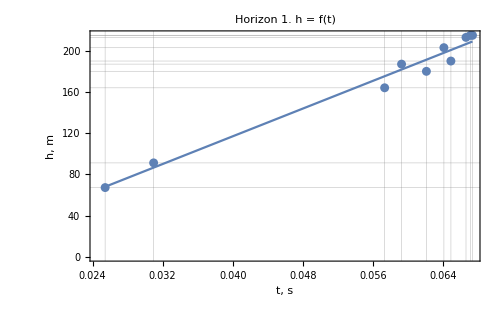
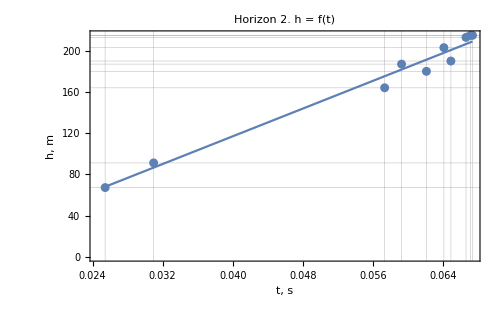

{}

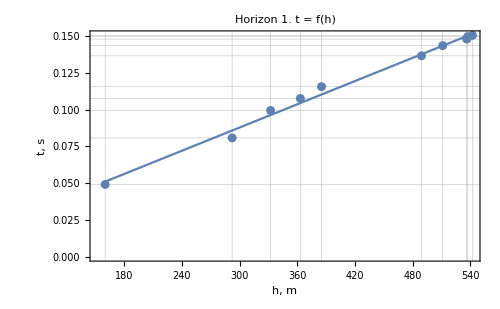
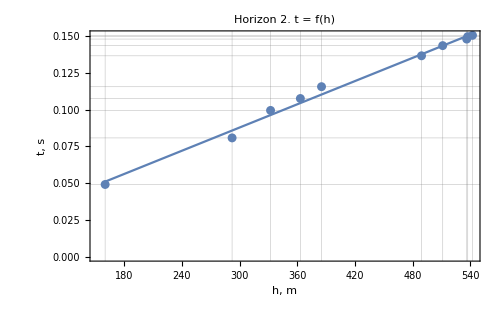

```mathematica
PlotHT[dplotDataHT1,dlmSetHT1, dt]
PlotVT[dplotDataVT1 ,dlmSetVT1, dt]
PlotTH[dplotDataTH1, dlmSetTH1, dh]
```

### Linear regression plots for set2

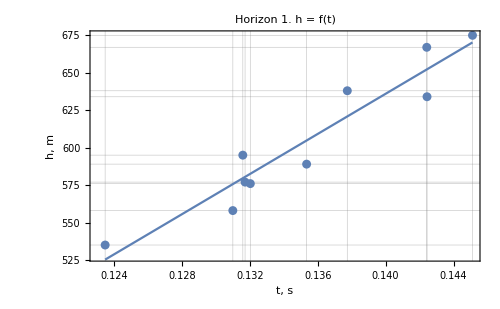

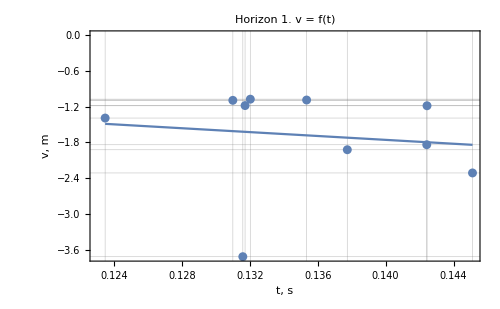

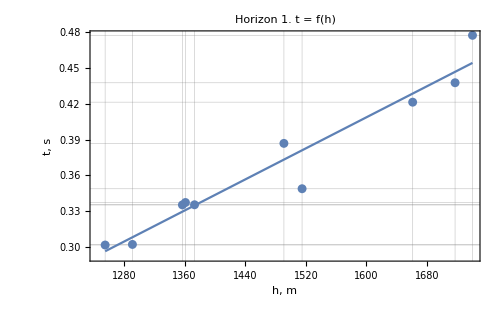

```mathematica
PlotHT[dplotDataHT2,dlmSetHT2, dt]
PlotVT[dplotDataVT2 ,dlmSetVT2, dt]
PlotTH[dplotDataTH2, dlmSetTH2, dh]
```

## Results for set1

```mathematica
Show[ListLinePlot[horizons, GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 1000,
					PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)], PlotStyle->Gray],
	ListLinePlot[dresultHT1, PlotStyle->{Pink}],
	ListLinePlot[dresultVT1 , PlotStyle->{Purple}],
	ListLinePlot[dresultTH1, PlotStyle->{Orange}],
ListLinePlot[dresultVave1, PlotStyle->{Brown}]
]
```

-Graphics-

### Results for set2

```mathematica
Show[ListLinePlot[horizons, GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 1000,
					PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)], PlotStyle->Gray],
	ListLinePlot[dresultHT2, PlotStyle->{Pink}],
	ListLinePlot[dresultVT2 , PlotStyle->{Purple}],
	ListLinePlot[dresultTH2, PlotStyle->{Orange}],
ListLinePlot[dresultVave2, PlotStyle->{Brown}]
]
```

-Graphics-